```mathematica
Integrate[1/(2 Pi)(a+b Cos[k])/(x+y Cos[k]),{k,-Pi,Pi}]
```

ConditionalExpression[b (Piecewise[{{1/y, !(Abs[(x-√(x^2-y^2))/y]<1⊻Abs[(x+√(x^2-y^2))/y]<1)}, {(1-x/(√(x^2-y^2)))/y, Abs[(x+√(x^2-y^2))/y]≥1&&Abs[(x-√(x^2-y^2))/y]<1}, {(1+x/(√(x^2-y^2)))/y, True}}])+a (Piecewise[{{-1/(√(x^2-y^2)), Abs[(x-√(x^2-y^2))/y]≥1&&Abs[(x+√(x^2-y^2))/y]<1}, {1/(√(x^2-y^2)), Abs[(x-√(x^2-y^2))/y]<1&&Abs[(x+√(x^2-y^2))/y]≥1}, {0, True}}]), ]

```mathematica
Integrate[1/(2 Pi)  b Cos[k]/(x+y Cos[k]),{k,-Pi,Pi}]
```

ConditionalExpression[b (Piecewise[{{1/y, !(Abs[(x-√(x^2-y^2))/y]<1⊻Abs[(x+√(x^2-y^2))/y]<1)}, {(1-x/(√(x^2-y^2)))/y, Abs[(x+√(x^2-y^2))/y]≥1&&Abs[(x-√(x^2-y^2))/y]<1}, {(1+x/(√(x^2-y^2)))/y, True}}]), ]

```mathematica
Inverse[{{1+1/a  p/(4J)(a+(z+J)^2),-1/a  p/(4J)(a-J^2+z^2)},{-1/a  p/(4J)(a-J^2+z^2),1+1/a p/(4J) (a+(z-J)^2)}}]
```

{{(1+(p (a+(-J+z)^2))/(4 a J))/(1+p/(2 J)+(J p)/(2 a)+p^2/(4 a)+(p z^2)/(2 a J)),(p (a-J^2+z^2))/(4 a J (1+p/(2 J)+(J p)/(2 a)+p^2/(4 a)+(p z^2)/(2 a J)))},{(p (a-J^2+z^2))/(4 a J (1+p/(2 J)+(J p)/(2 a)+p^2/(4 a)+(p z^2)/(2 a J))),(1+(p (a+(J+z)^2))/(4 a J))/(1+p/(2 J)+(J p)/(2 a)+p^2/(4 a)+(p z^2)/(2 a J))}}

```mathematica
Simplify[1+p/(2 J)+(J p)/(2 a)+p^2/(4 a)+(p z^2)/(2 a J)]
```

(2 a (2 J+p)+p (2 J^2+J p+2 z^2))/(4 a J)

```mathematica
2 a (2 J+p)+p (2 J^2+J p+2 z^2)/.{a->Sqrt[(z^2-J^2)^2-(2Jq)^2]}
```

p (2 J^2+J p+2 z^2)+2 (2 J+p) √(-4 Jq^2+(-J^2+z^2)^2)

```mathematica
Solve[%==0,z]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z→-√(J^4/(J^2+J p)+(J^3 p)/(J^2+J p)+(J^2 p^2)/(2 (J^2+J p))+(J p^3)/(8 (J^2+J p))-1/(8 (J^2+J p))(√(256 J^4 Jq^2+512 J^3 Jq^2 p+64 J^6 p^2+320 J^2 Jq^2 p^2+96 J^5 p^3+64 J Jq^2 p^3+52 J^4 p^4+12 J^3 p^5+J^2 p^6)))},{z→√(J^4/(J^2+J p)+(J^3 p)/(J^2+J p)+(J^2 p^2)/(2 (J^2+J p))+(J p^3)/(8 (J^2+J p))-1/(8 (J^2+J p))(√(256 J^4 Jq^2+512 J^3 Jq^2 p+64 J^6 p^2+320 J^2 Jq^2 p^2+96 J^5 p^3+64 J Jq^2 p^3+52 J^4 p^4+12 J^3 p^5+J^2 p^6)))},{z→-√(J^4/(J^2+J p)+(J^3 p)/(J^2+J p)+(J^2 p^2)/(2 (J^2+J p))+(J p^3)/(8 (J^2+J p))+1/(8 (J^2+J p))(√(256 J^4 Jq^2+512 J^3 Jq^2 p+64 J^6 p^2+320 J^2 Jq^2 p^2+96 J^5 p^3+64 J Jq^2 p^3+52 J^4 p^4+12 J^3 p^5+J^2 p^6)))},{z→√(J^4/(J^2+J p)+(J^3 p)/(J^2+J p)+(J^2 p^2)/(2 (J^2+J p))+(J p^3)/(8 (J^2+J p))+1/(8 (J^2+J p))(√(256 J^4 Jq^2+512 J^3 Jq^2 p+64 J^6 p^2+320 J^2 Jq^2 p^2+96 J^5 p^3+64 J Jq^2 p^3+52 J^4 p^4+12 J^3 p^5+J^2 p^6)))}}

```mathematica
√(J^4/(J^2+J p)+(J^3 p)/(J^2+J p)+(J^2 p^2)/(2 (J^2+J p))+(J p^3)/(8 (J^2+J p))-1/(8 (J^2+J p))(√(256 J^4 J q^2+512 J^3 J q^2 p+64 J^6 p^2+320 J^2 J q^2 p^2+96 J^5 p^3+64 J  J q^2 p^3+52 J^4 p^4+12 J^3 p^5+J^2 p^6)))/.{J->1, p->2*-0.4}
```

√(2.28-0.625 √(9.43718+18.432 q^2))

```mathematica
1-Sqrt[q^2+p^2]/.{p->-0.4}
```

1-√(0.16+q^2)

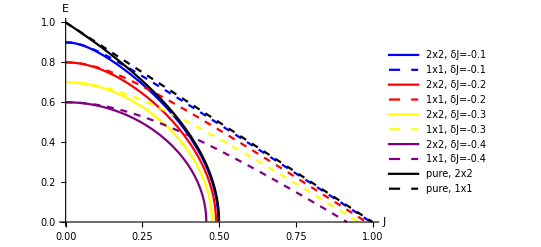

```mathematica
Plot[{√(1.02375-0.15625 √(1.8714240000000002+165.88799999999998 q^2)), 1-√(0.01+q^2), √(1.12-0.20833333333333334 √(5.308416000000001+98.304 q^2)), 1-√(0.04000000000000001+q^2), √(1.3824999999999998-0.3125 √(8.156735999999999+50.17599999999999 q^2)), 1-√(0.09+q^2), √(2.2800000000000002-0.6250000000000001 √(9.437184+18.431999999999988 q^2)), 1-√(0.16000000000000003+q^2), Sqrt[1-2q], 1-q},{q,0,1},PlotStyle->{Blue,{Blue,Dashed},Red, {Red, Dashed},Yellow, {Yellow, Dashed}, Purple, {Purple, Dashed}, Black, {Black, Dashed}},PlotRange->{0,1},PlotLegends->Placed[{"2x2, δJ=-0.1","1x1, δJ=-0.1","2x2, δJ=-0.2","1x1, δJ=-0.2","2x2, δJ=-0.3","1x1, δJ=-0.3", "2x2, δJ=-0.4", "1x1, δJ=-0.4", "pure, 2x2", "pure, 1x1"}, Above], AxesLabel->{J,"E"}]
```

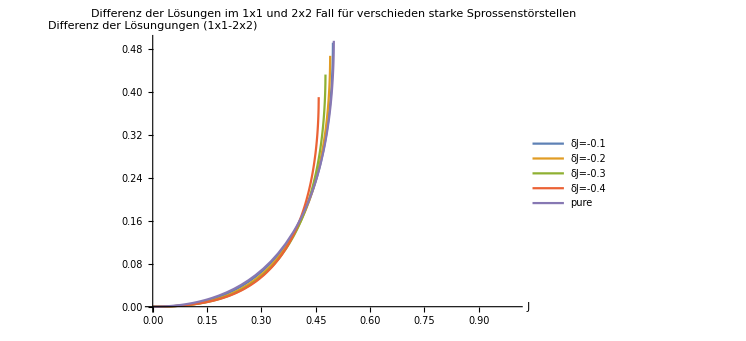

```mathematica
Plot[{-√(1.02375-0.15625 √(1.8714240000000002+165.88799999999998 q^2))+(1-√(0.01+q^2)),-√(1.12-0.20833333333333334 √(5.308416000000001+98.304 q^2))+(1-√(0.04000000000000001+q^2)),-√(1.3824999999999998-0.3125 √(8.156735999999999+50.17599999999999 q^2))+ 1-√(0.09+q^2),-√(2.2800000000000002-0.6250000000000001 √(9.437184+18.431999999999988 q^2))+ 1-√(0.16000000000000003+q^2), -Sqrt[1-2q]+1-q},{q,0,1},PlotLegends->Placed[{"δJ=-0.1","δJ=-0.2","δJ=-0.3", "δJ=-0.4", "pure"}, Above],AxesLabel->{J,"Differenz der Lösungungen (1x1-2x2)"},PlotLabel->"Differenz der Lösungen im 1x1 und 2x2 Fall für verschieden starke Sprossenstörstellen"]
```